# Gravitational Wave

## Prepare

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
<<anybubble.m
<<powell.m
Options[FindBubble]
```

/Users/isaac/Dropbox/Research_Project/2021-9-Local_EWBG_parity/02-Analysis/running-approach

{Verbose→False,SpaceTimeDimension→3,StartAnalyticFraction→1/100,EndAnalyticFraction→1/100,MaxIntervalGrowth→30,MaxReadjustments→20,InitialProfilePoints→{},PowellVerbosity→1,MaxIterations→500,AccuracyGoal→Automatic,WorkingPrecision→MachinePrecision}

## Running

```mathematica
sw = √0.23116;
cw = √(1 - sw^2);
mZ = 91.1876; 
mW = 80.399;
(*mtpole = 173.1-0.7*2.5;*)
GF = 1.16637 10^-5;
v=1/(√(√2*GF));
mb=4.19;mc=1.27;ms=0.1;
α0=1/137.035999679;
ΔαhmZ=0.02758;
αmZ= α0/(1-0.03150-ΔαhmZ+0.00007);
αsmZ=0.1181+0.0011*(1);

Mpl=2.4*10^18;(*Planck mass*)
mhpole=125.18+0.16*(0);

ye=2.8*10^-6;
yμ=5.9*10^-4;
yτ=1.0*10^-2;
yd=1.6*10^-5/2;
ys=3.1*10^-4/2;
yb=1.6*10^-2/2;
yu=7.4*10^-6/2;
yc=3.6*10^-3/2;
```

```mathematica
κ=1/(16 π^2)(*Phase space factor*);
Nf=6;(*number of flavor why?*)
Ng=3;(*number of generation*)
z3=Zeta[3];
(*QCD*)
CA=3;(*Casimir operator Subscript[C, A]=Subscript[C, 2](adj)*)
CF=4/3;(*Casimir operator Subscript[C, F]=Subscript[C, 2](fund)*)
TR=1/2;(*Index Subscript[T, R](fund)*)
dR=3;(*dimension of representation, can be understood as color factor*)
SmoothUnitStep[x_]:=ArcTan[10x]/π+1/2;
g1mZ=(√(4π αmZ))/cw;
g2mZ=(√(4π αmZ))/sw;
g3mZ=√(4π*αsmZ);
αsmZ=0.1179;

(*Measured pole masses*)
mhpole=125.10;
mtpole=172.76;

(*MSbar couplings*)
λmtpole:=0.12604+0.00206*(mhpole-125.15)-0.00004(mtpole-173.34);
ytmtpole:=0.93690+0.00556(mtpole-173.34)-0.00003(mhpole-125.15)-0.00042((αsmZ-0.1184)/0.0007);
g3mtpole=1.1666+0.00314((αsmZ-0.1184)/0.0007)-0.00046(mtpole-173.34);
g2mtpole=0.64779+0.00004(mtpole-173.34)+0.00011*(mW-80.384)/0.014;
g1mtpole=0.35830+0.00011(mtpole-173.34)-0.00020*(mW-80.384)/0.014;
```

```mathematica
βyt[λ_,yt_,g3_,g2_,g1_,yN_]:=2yt(κ yt^2(3/4+1/2 dR)+κ g3^2(-3CF)+3 κ^2 λ^2+(-6)κ^2 yt^2 λ+κ^2 yt^4(3/4-9/4 dR)+κ^2 g3^2 yt^2(6CF+5/2 CF dR)+κ^2 g3^4(-3/2 CF^2-97/6 CA CF+10/3 Nf TR CF)+κ^3 λ^3(-18)+κ^3 yt^2 λ^2(285/8-45/4 dR)+κ^3 yt^4 λ(63/2+45/2 dR)+κ^3 yt^6(-345/32+107/32 dR+39/16 dR^2+9/4 z3+3/2 z3 dR)+κ^3 g3^2 yt^2 λ(6CF)+κ^3 g3^2 yt^4(-57/2 CF-81/8 CF dR)+κ^3 g3^4 yt^2(471/16 CF^2-119/8 CF^2 dR+25TR CF+717/16 CA CF+77/4 CA CF dR-33/4 Nf TR CF-4Nf TR CF dR-27z3 CF^2+18z3 CF^2 dR-27/2 z3 CA CF-9 z3 CA CF dR)+κ^3 g3^6(-129/2 CF^3+129/4 CA CF^2-11413/108 CA^2 CF+46Nf TR CF^2+556/27 Nf CA TR CF+140/27 Nf^2 TR^2 CF-48z3 Nf TR CF^2+48z3 Nf CA TR CF))+
yt κ(-9/4 g2^2-17/12 g1^2)+
yt κ^2(5/2 yt^2(17/12 g1^2+9/4 g2^2)+yt^2(223/48 g1^2+135/16 g2^2)+25/9 g1^4(9/200+29/45 Ng)+58/57 g1^4*2-3/4 g1^2 g2^2+19/9 g1^2 g3^2-(35/4-Ng)g2^4+9 g2^2 g3^2);
βg3[λ_,yt_,g3_,g2_,g1_,yN_]:=2g3(κ g3^2(-11/6 CA+2/3 Nf TR)+κ^2 g3^2 yt^2(-2TR)+κ^2 g3^4(-17/3 CA^2+2Nf TR CF+10/3 Nf CA TR)+κ^3 g3^2 yt^4(9/2 TR+7/2 TR dR)+κ^3 g3^4 yt^2(-3TR CF-12CA TR)+κ^3 g3^6(-2857/108 CA^3-Nf TR CF^2+205/18 Nf CA TR CF+1415/54 Nf CA^2 TR-22/9 Nf^2 TR^2 CF-79/27 Nf^2 CA TR^2))+g3^3 κ^2(11/6 g1^2+9/2 g2^2);
βg1[λ_,yt_,g3_,g2_,g1_,yN_]:=-g1^3 κ(-1/6-20/9 Ng+2/3*2)+g1^3 κ^2 5/3(199/30 g1^2+6/5*2 g1^2+27/10 g2^2+44/5 g3^2-17/10 yt^2);
βg2[λ_,yt_,g3_,g2_,g1_,yN_]:=-g2^3 κ(43/6-4/3 Ng)+g2^3 κ^2(3/2 g1^2+35/6 g2^2+12 g3^2-3/2 yt^2);
βλ[λ_,yt_,g3_,g2_,g1_,t_,yN_]:=2(12κ λ^2+2κ yt^2 λ dR+κ yt^4(-dR)+κ (yN SmoothUnitStep[t-Log[800/mZ]])^4(-2)+κ^2 λ^3(-156)+κ^2 yt^2 λ^2(-24dR)+κ^2 yt^4 λ(-1/2 dR)+κ^2 yt^6(5dR)+κ^2 g3^2 yt^2 λ(10CF dR)+κ^2 g3^2 yt^4(-4CF dR)+κ^3 λ^4(3588+2016z3)+κ^3 yt^2 λ^3(291dR)+κ^3 yt^4 λ^2(789/2 dR-36 dR^2+252z3 dR)+κ^3 yt^6 λ(-1881/8 dR+80 dR^2-66z3 dR)+κ^3 yt^8(13/2 dR-195/8 dR^2-12z3 dR)+κ^3 g3^2 yt^2 λ^2(-306CF dR+288z3 CF dR)+κ^3 g3^2 yt^4 λ(895/4 CF dR-324 z3 CF dR)+κ^3 g3^2 yt^6(-19/2 CF dR+60z3 CF dR)+κ^3 g3^2 yt^2 λ(-119/2 CF^2 dR+77CA CF dR-16Nf TR CF dR+72z3 CF^2 dR-36z3 CA CF dR)+κ^3 g3^4 yt^4(131/2 CF^2 dR+48TR CF dR-109/2 CA CF dR+10Nf TR CF dR-48z3 CF^2 dR+24z3 CA CF dR))+κ/2(-(3 g1^2+9 g2^2)2λ+9/4(1/3 g1^4+2/3 g1^2 g2^2+g2^4))+κ^2/2((54 g2^2+18 g1^2)4 λ^2-((313/8-10Ng)g2^4-39/4 g2^2 g1^2-(687/200+2Ng)25/9 g1^4+60/19*2 g1^4)2λ+(497/8-8Ng)g2^6-(97/40+8/5 Ng)5/3 g2^4 g1^2-(717/200+8/5 Ng)25/9 g2^2 g1^4-(531/1000+24/25 Ng)125/27 g1^6-1728/505*2 g1^6-8/3 g1^2 2 yt^4-9/2 g2^4 yt^2+5/3 g1^2(63/5 g2^2-57/10 g1^2)yt^2+10 *2 λ yt^2(17/12 g1^2+9/4 g2^2));
```

```mathematica
vR=100000;
yN=0.8;
aB=Exp[3.91];
aF=Exp[1.14];
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR=λ[vR];
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-8 mNsq^2);
DD=1/(8 vR^2)(2mWsq+mZsq+2mtsq+4/3 mNsq);
EE=1/(4π vR^3)(2 mWsq^(3/2)+mZsq^(3/2));
λT[T_]:=λvR-3/(16 π^2 vR^4)(2 mWsq^2 Log[mWsq/(aB T^2)]+mZsq^2 Log[mZsq/(aB T^2)]-4 mtsq^2 Log[mtsq/(aF T^2)]-8/3 mNsq^2 Log[mNsq/(aF T^2)]);
mgaugevR=({{g2[vR]^2 x1^2/4+11/6 g2[vR]^2 x2^2, -g1[vR] g2[vR] x1^2/4}, {-g2[vR]g1[vR] x1^2/4, g1[vR]^2 x1^2/4+14/9 g1[vR]^2 x2^2}});
gaugeLvR=Eigenvalues[mgaugevR]//FullSimplify;
mWL[ϕ_,T_]:=1/4 g2[vR]^2 ϕ^2+11/6 g2[vR]^2 T^2;
mBL[ϕ_,T_]:=gaugeLvR[[1]]/.{x1->ϕ,x2->T};
mZL[ϕ_,T_]:=gaugeLvR[[2]]/.{x1->ϕ,x2->T};
resum[ϕ_,T_]:=T/(12π)(2((mWsq ϕ^2/vR^2)^(3/2)-mWL[ϕ,T]^(3/2))+((mZsq ϕ^2/vR^2)^(3/2)-(mZL[ϕ,T])^(3/2))-Abs[mBL[ϕ,T]]^(3/2));
T0=√(1/(4DD)(mHvR^2-8B vR^2));
Veff[ϕ_,T_]:=DD (T^2-T0^2)ϕ^2-EE T ϕ^3+λT[T]/4 ϕ^4+resum[ϕ,T]-resum[10^-10,T];
T1=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T0,1.2T0,0.1T0}]];
T2=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T1-0.1T0,T1,0.01T0}]];
T3=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T2-0.01T0,T2,0.001T0}]];
T4=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T3-0.001T0,T3,0.0001T0}]];
Tc=Catch[Do[If[FindMinimum[Veff[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T4-0.0001T0,T4,0.00001T0}]];
vev=ϕ/.FindMinimum[Veff[ϕ,Tc],{ϕ,vR}][[2]];
strength=vev/Tc
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

1.06411

```mathematica
λvR
```

0.000112659

```mathematica
((1/6)^2*3*2*2*2+(1/2)^2*3*2*2+(1/6)^2*3*2*2+(1/3)^2*3*2+(2/3)^2*3*2)/6 (*Integrate out all the singlet heavy fermion except for the top quark*)
```

11/9

```mathematica
1/3+11/9
```

14/9

## GW

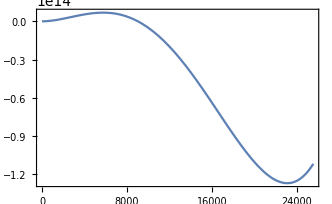

```mathematica
Tplot=0.99703Tc;
Plot[Veff[ϕ,Tplot],{ϕ,0,1.4Tc}]
```

```mathematica
fitting=Table[{ϕ,Veff[ϕ,Tplot]},{ϕ,1,1.4Tplot,200}];
Vfit[ϕ_]=Fit[fitting,{1,ϕ,ϕ^2,ϕ^3,ϕ^4,ϕ^5,ϕ^6,ϕ^7,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
xr=x/.Minimize[{Vfit[x]-Vfit[0],{0.8Tplot<x<1.4Tplot}},x][[2]];
SbyT=(FindBubble[Vfit[x[1]]-Vfit[0],x,{xr},{0}]/Tplot)[[1]]
```

.........................

140.616

```mathematica
Tn=Tplot;
gstar=143;
bouncelist=Table[{
Clear[fitting,Vfit];
fitting=Table[{ϕ,Veff[ϕ,T1]},{ϕ,1,1.5T1,200}];
Vfit[ϕ_]=Fit[fitting,{1,ϕ,ϕ^2,ϕ^3,ϕ^4,ϕ^5,ϕ^6,ϕ^7,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
xr=x/.Minimize[{Vfit[x]-Vfit[0],{0.8T1<x<1.4T1}},x][[2]];
T1,
SbyT=(FindBubble[Vfit[x[1]]-Vfit[0],x,{xr},{0}]/T1)[[1]],
δV=Minimize[{Vfit[ϕ]-Vfit[0],{0.8T1<ϕ<1.4T1}},ϕ][[1]]
}
,{T1,Tn-0.5,Tn+0.5,0.1}]
```

............................................................................................................................................................................................................................

{{18176.8,138.524,-1.2833×10^14},{18176.9,138.959,-1.2806×10^14},{18177.,139.396,-1.2779×10^14},{18177.1,139.746,-1.2752×10^14},{18177.2,140.181,-1.2725×10^14},{18177.3,140.616,-1.2698×10^14},{18177.4,141.053,-1.26711×10^14},{18177.5,141.504,-1.26441×10^14},{18177.6,141.965,-1.26172×10^14},{18177.7,142.511,-1.25902×10^14},{18177.8,142.964,-1.25633×10^14}}

```mathematica
actionlist=bouncelist[[All,{1,2}]];
latentheat=bouncelist[[All,{1,3}]];
```

```mathematica
Clear[fitting,Vfit];
fitting=Table[{ϕ,Veff[ϕ,Tn]},{ϕ,1,1.5Tn,200}];
Vfit[ϕ_]=Fit[fitting,{1,ϕ,ϕ^2,ϕ^3,ϕ^4,ϕ^5,ϕ^6,ϕ^7,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
ΔV=Minimize[{Vfit[v]-Vfit[0]},{0.8Tn<v<1.4Tn}][[1]]
S3T[T_]=Interpolation[actionlist][T];
deltaV[T_]=Interpolation[latentheat][T];
ρrad=π^2/30 gstar Tn^4;
α=(-ΔV+1/4 Tn*deltaV'[Tn])/ρrad
βH=Tn*S3T'[Tn]
```

4.10074×10^10

0.00238667

79144.6

```mathematica
myTicks[lower_,upper_,step_]:=Flatten[Module[{Local=#,LocalTicks},LocalTicks=Log[10,Range[10^(#-1),10^#,(10^#-10^(#-1))/(10-1)]];
Join[{#,""}&/@Most[LocalTicks],{{Last[LocalTicks],Which[Last[LocalTicks]==0,1,Last[LocalTicks]==1,10,True,Power[10,ToString[Last[LocalTicks]]]],{0.03,0}(*longer ticks*)}}]]&/@Range[lower,upper,step],1];
```

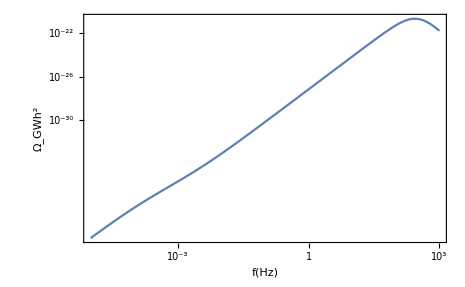

```mathematica
fsou[vb_,βH_,Tn_]:=1.9*10^(-5)*(100/100)^(1/6)*(Tn/100)*(βH)/vb;
κa[α_]:=α/(0.73+0.083Sqrt[α]+α);
Ωsou[f_,vb_,α_,βH_,Tn_]:=2.65*10^(-6)*vb*(100/100)^(1/3)/βH*(κa[α]*α/(1+α))^2*(7^(7/2)*(f/fsou[vb,βH,Tn])^3/(4+3(f/fsou[vb,βH,Tn])^2)^(7/2));
κtur[α_]=.05*κa[α];
(*Plasma turbulence*)
ftur[vb_,βH_,Tn_]=2.7/vb*10^(-5)*βH*(Tn/100)*(100/100)^(1/6);
(*A peak frequency of the turbulence*)
hstar[Tn_]:=16.5*10^(-6)*(Tn/100)*(100/100)^(1/6);
(*Hubble paramter at Subscript[T, n]*)
Ωtur[f_,vb_,α_,βH_,Tn_]:=3.35*10^(-4)/βH*(κtur[α]*α/(1+α))^(3/2)*(100/100)^(1/3)*vb*(f/ftur[vb,βH,Tn])^3/(1+f/(ftur[vb,βH,Tn]))^(11/3)/(1+8*Pi*f/hstar[Tn]);signal=Plot[Log10[Ωsou[10^logf,1.0,α,βH,Tn]+Ωtur[10^logf,1.0,α,βH,Tn]],{logf,-5,3},Axes->None,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["f(Hz)",FontFamily->"Times",FontSize->18],Style["Ω_GWh^2",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},FrameTicks->{{myTicks[-30,-7,2],None},{myTicks[-6,6,1],None}}]
```

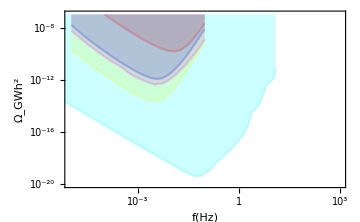

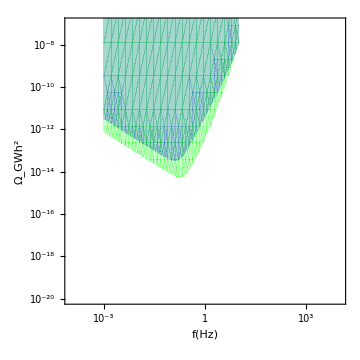

```mathematica
eLISAC4=Import[NotebookDirectory[]<>"data/LISAC4.csv"];
eLISAC3=Import[NotebookDirectory[]<>"data/LISAC3.csv"];
eLISAC2=Import[NotebookDirectory[]<>"data/LISAC2.csv"];
eLISAC1=Import[NotebookDirectory[]<>"data/LISAC1.csv"];
UD=Import[NotebookDirectory[]<>"data/UltimateDecigo-Sachiko.csv"];
eLISAandUD=ListLinePlot[{eLISAC4,eLISAC3,eLISAC2,eLISAC1,UD},Filling->Top,ImageSize->Medium,Axes->None,PlotRange->{{-5,3},{-20,-7}},FrameTicks->{{myTicks[-20,-7,2],None},{myTicks[-6,6,1],None}},FrameTicksStyle->{16,Black,FontFamily->"Times"},FrameLabel->{Style["f(Hz)",FontFamily->"Times",FontSize->18],Style["Ω_GWh^2",FontFamily->"Times",FontSize->18]},PlotStyle->{{RGBColor[1,0,0],Opacity[0.2]},{RGBColor[0,0,1],Opacity[0.2]},{RGBColor[1,0,1],Opacity[0.2]},{RGBColor[1,1,0],Opacity[0.2]},{RGBColor[0,1,1],Opacity[0.2]}},Background->White,LabelStyle->{FontFamily->"Times",FontSize->16},PlotRangePadding->None]
DECIGOandBBO=RegionPlot[{y>Log10[(3*10^17)^2*2*Pi^2/3*(10^f)^3(7.05*10^(-48)*(1+(10^f/7.36)^2)+4.8*10^(-51)/10^(4f)/(1+(10^f/7.36)^2)+5.33*10^(-52)10^(-4f))],y>Log10[(3*10^17)^2*2*Pi^2/3*(10^f)^3(2*10^(-49)*10^(2f)+4.58*10^(-49)+1.26*10^(-51)*10^(-4f))]},{f,-3,1},{y,-30,0},ImageSize->Medium,Axes->None,PlotRange->{{-4,4},{-20,-7}},FrameTicks->{{myTicks[-20,-7,2],None},{myTicks[-6,6,1],None}},FrameTicksStyle->{16,Black,FontFamily->"Times"},FrameLabel->{Style["f(Hz)",FontFamily->"Times",FontSize->16],Style["Ω_GWh^2",FontFamily->"Times",FontSize->16]},Background->White,LabelStyle->{FontFamily->"Times",FontSize->16},PlotRangePadding->None,PlotStyle->{{RGBColor[0,0,1],Opacity[0.2]},{RGBColor[0,1,0],Opacity[0.2]}},BoundaryStyle->None]
```

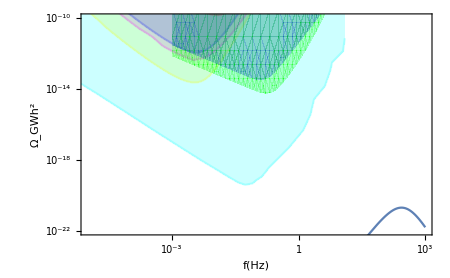

```mathematica
Show[signal,eLISAandUD,DECIGOandBBO,PlotRange->{{-5,3},{-22,-10}},ImageSize->450]
```